#### Determination of oscillation periods of biological clocks Authors: Jesús Hernández-Trujillo, Marco Franco-Pérez, Alejandro Pisanty-Baruch

#### Mathematica code for the computation of the oscillation period of the segmentation clock based on the HES7 gene expression. Data from Extended Figure 2 (spheroidal all area, experiment 1) of “Recapitulating the human segmentation clock with pluripotent stem cells”, doi:10.1038/s41586-020-2144-9.

```mathematica
ClearAll["Global`*"]; SetDirectory[NotebookDirectory[]];
```

#### A. Data import.

```mathematica
(*
Retrieval of the raw data for the experimental gene expression values as a function of time from a csv file. Definition of basic variables.
*)
```

```mathematica
rawdata=Import["hes7.csv","csv","HeaderLines"->1];
ndat=Dimensions[rawdata][[1]];
 t0 = rawdata⟦1, 1⟧; tf = rawdata⟦ndat, 1⟧; Δt =( tf - t0)/(ndat-1);
timegrid=rawdata[[All,1]];
activity=rawdata[[All,2]];
```

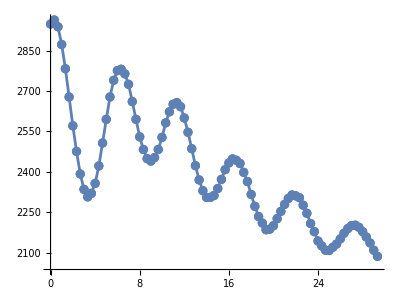

```mathematica
ListLinePlot[Transpose[{timegrid/60,activity}],Mesh->Full,TicksStyle->Directive[FontSize->12],AspectRatio->0.75]
```

#### Part 1 Direct Fourier transform of the raw data.

```mathematica
(*
This step should be included whenever the raw data are not provided on a regular grid. For example an interpolation with cubic splines can be carried out and plotted as follows:
f=Interpolation[rawdata];
   a=Plot[f[x],{x,t0,tf}]; b=ListPlot[rawdata];
   Show[{a,b}]
 timegrid=Table[x,{t0,tf,Δt}];
   activity=Table[f[x],{t0,tf,Δt}];
*)
```

```mathematica
spectrum=Abs[Fourier[activity]]^2;  (* Power spectrum *)
```

```mathematica
M=Dimensions[spectrum][[1]];
Δt/=60; (* Conversion from minutes to hours *)
T=M Δt;
```

```mathematica
ωvals=Table[2 Pi i/T,{i,0,M/2-1}];  (* Frequency spectrum *)
spectrumb=Table[spectrum[[i]],{i,1,M/2}]; (* Only half of the spectrum is required *)
```

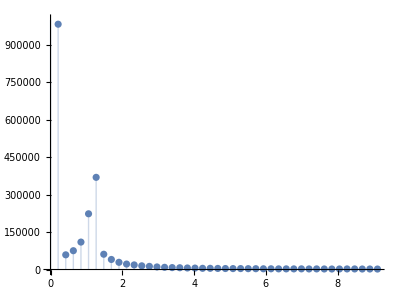

```mathematica
ListPlot[Transpose[{ωvals,spectrumb}],PlotRange->{0,1000000},Filling->Axis,TicksStyle->Directive[FontSize->12],AspectRatio->0.75]
```

```mathematica
pairs=N[Transpose[{ωvals,spectrumb}]];
```

```mathematica
(* The eight most relevant frequencies are displayed next. *)
```

```mathematica
For[i=2,i<=9,i++,
Print["ω",i-1,"=", pairs[[i,1]],"  amplitude=",pairs[[i,2]]]
]
```

ω1=0.211793  amplitude=983097.

ω2=0.423586  amplitude=58852.3

ω3=0.635378  amplitude=75350.

ω4=0.847171  amplitude=109956.

ω5=1.05896  amplitude=223330.

ω6=1.27076  amplitude=369381.

ω7=1.48255  amplitude=61177.

ω8=1.69434  amplitude=40270.2

```mathematica
periods=Table[j,{j,1,M/2}];
(*
Note that this list also includes ω=0, in Mathematica the first element of an array has the index value = 1.
*)

For[i=1,i<=M/2,i++,
If[pairs[[i,1]]!=0,periods[[i]]=2 Pi/pairs[[i,1]]]]
```

```mathematica
(*
τ1 corresponds to the entire data set and is discarded for it assumes it defines a period. The most relevant periods are τ5 and τ6.
*)
```

```mathematica
For[i=2,i<=9,i++,
Print["τ",i-1,"=",periods[[i]],"    amplitude=",pairs[[i,2]]]
]
```

τ1=29.6667    amplitude=983097.

τ2=14.8333    amplitude=58852.3

τ3=9.88889    amplitude=75350.

τ4=7.41667    amplitude=109956.

τ5=5.93333    amplitude=223330.

τ6=4.94444    amplitude=369381.

τ7=4.2381    amplitude=61177.

τ8=3.70833    amplitude=40270.2

#### Part 2 Scaling of raw data + detrending

```mathematica
maxa=Max[activity]; activity/=maxa;
aavg=N[Mean[activity]]; (* Average value of the data set. *)
arel=100 (activity-aavg)/aavg; (* Scaling is carried according to Eq.(7) of the article. *)
areldetrend=Differences[arel]; (* Detrending by first order differences, Eq.(5). *)
```

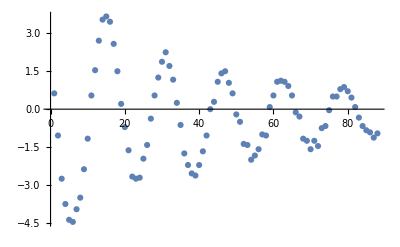

```mathematica
ListPlot[areldetrend]
```

#### Direct Fourier transform of the detrended data.

```mathematica
detrendedspectrum=Abs[Fourier[areldetrend]]^2;
```

```mathematica
Mdetrended=Dimensions[detrendedspectrum][[1]]; (* The data set has been reduced by one value after the detrending of the raw set. *)
```

```mathematica
Tdetrended= Mdetrended Δt;
spectrumc=Table[detrendedspectrum[[i]],{i,1,M/2}]; 
ωdetrended=Table[2 Pi i/Tdetrended,{i,0,Mdetrended/2-1}];
```

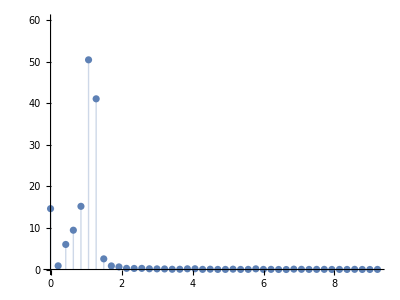

```mathematica
ListPlot[Transpose[{ωdetrended,spectrumc}],PlotRange->{0,60},Filling->Axis,TicksStyle->Directive[FontSize->12],AspectRatio->0.75]
```

```mathematica
Position[spectrumc,Max[spectrumc]] (* The fifth is most relevant frecuency. *)
```

{{6}}

```mathematica
pairsc=N[Transpose[{ωdetrended,spectrumc}]];
```

```mathematica
(* The eight most relevant frequencies are displayed next. *)
```

```mathematica
For[i=2,i<=9,i++,
Print["ω",i-1,"=", pairsc[[i,1]],"  amplitude=",pairsc[[i,2]]
]]
```

ω1=0.214199  amplitude=0.882745

ω2=0.428399  amplitude=6.02348

ω3=0.642598  amplitude=9.45113

ω4=0.856798  amplitude=15.195

ω5=1.071  amplitude=50.4211

ω6=1.2852  amplitude=41.0452

ω7=1.4994  amplitude=2.55947

ω8=1.7136  amplitude=0.860424

```mathematica
periodsc=Table[j,{j,1,Mdetrended/2}];(* Note that this list also includes ω=0. *)

For[i=1,i<=Mdetrended/2,i++,
If[pairsc[[i,1]]!=0,periodsc[[i]]=2 Pi/pairsc[[i,1]]]]
```

```mathematica
For[i=2,i<=9,i++,
Print["τ",i-1,"=",periodsc[[i]],"    amplitude=",pairsc[[i,2]]]
]
```

τ1=29.3333    amplitude=0.882745

τ2=14.6667    amplitude=6.02348

τ3=9.77778    amplitude=9.45113

τ4=7.33333    amplitude=15.195

τ5=5.86667    amplitude=50.4211

τ6=4.88889    amplitude=41.0452

τ7=4.19048    amplitude=2.55947

τ8=3.66667    amplitude=0.860424

```mathematica
(*
The most relevant periods are τ5 and τ6.
*)
```

#### Part 3 Non linear fit of the detrended set.

```mathematica
timegrid2=Table[timegrid[[i]]/60,{i,2,ndat}]; (* Discard first time value. *)
detrendtable=Table[{timegrid2[[i]],areldetrend[[i]]},{i,1,Dimensions[areldetrend][[1]]}];  (* Time vs. scaled detrended activity. *)
```

```mathematica
model=A Exp[-γ t] Sin[ω t+ ϕ]; (* Underdamped oscillator, Eq.(6). *)
underdamped=FindFit[detrendtable,model,{{A,3},{γ,0.001},{ω,0.2},{ϕ,1.3}},t]
```

{A→-4.78673,γ→0.0624793,ω→1.16108,ϕ→-0.854104}

```mathematica
graph1=ListLinePlot[detrendtable,Mesh->Full,TicksStyle->Directive[FontSize->20],AspectRatio->0.75];
```

```mathematica
graph2=Plot[Evaluate[model/.underdamped],{t,timegrid2[[1]],timegrid2[[-1]]},PlotStyle->{Black,Thickness[0.004]},TicksStyle->Directive[FontSize->20],AspectRatio->0.85];
```

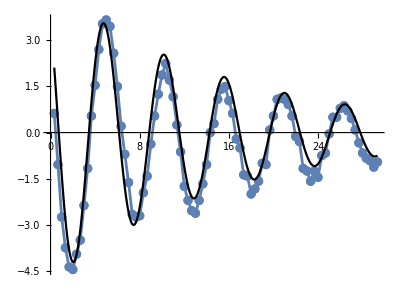

```mathematica
Show[graph1,graph2]
```

```mathematica
{A,γ,ϕ,ω}={A,γ,ϕ,ω}/.underdamped; (* ω is the angular frequency. *)
```

```mathematica
2 Pi/ω (* Oscillation period. *)
```

5.41151